```mathematica
GraphicsRow[(ArrayPlot[#,
ColorRules->{0->White,
1->{{"[◼]", "SecondLawColors"}}["Reds",3],
2->{{"[◼]", "SecondLawColors"}}["Reds",1]
},
FrameStyle->GrayLevel[0.7],
ImageSize->{100, Automatic}]&@(Take[First[#],{180,220}]&/@ResourceFunction["BlockCellularAutomaton"][{{
{1,0}->{0,1},{0,1}->{1,0},{1,2}->{0,2},
{2,1}->{2,0},{2,0}->{1,2},{0,2}->{2,1},
{1,1}->{2,2},{0,0}->{0,0},{2,2}->{1,1}},2},
{CenterArray[#,400],0},100]))&/@Table[
Table[2,x],{x,1,11,2}],ImageSize->{770, Automatic},Spacings->15]
```

-Graphics-

Figure 1. An example of a system where each of the parts is following a simple rule, but global structure still emerges. This is a hypergraph rewriting system, where each frame

```mathematica
SeedRandom[1111];
rand=RandomSample[{{"[◼]", "allperts"}}[CellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{102,{-200,200}}],4],400];Magnify[Module[{ru={299459058088077823758143088095350287424,4,1}},FeatureSpacePlot[With[{pca={{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{102,{-200,200}},#,"ReturnPerturbations"->False]},Rasterize[{{"[◼]", "PlotCA"}}[pca]]->{{"[◼]", "PlotCA"}}[pca,"Trim"->{3,None}]]&/@rand,LabelingSize->100,PlotStyle->AbsolutePointSize[9],Frame->True,FrameTicks->None,FrameStyle->Gray,RandomSeeding->64453,PerformanceGoal->"Static",ImageSize->2000]],.31]
```

-Graphics-

Figure 2. 
the tracking of individual molecules over time and illustrates how individual molecules can be tracked in causal relationships. 
An

This graph shows a reaction network which illustrates how individual molecules can be tracked in a causal relationship over time. This is monoterpene biosynthesis starting from geraniol out to six steps. 



This monoterpene biosynthesis starting from geraniol out to six steps

This graph shows the interact between individual molecules. 
 example of preliminary experiments on the behavior of large molecules using ideas from the Wolfram Physics Project. This is a partial token-event graph of monoterpene biosynthesis starting from geraniol out to six steps.

In making this connection, we hope to provide insight into the prediction

In making this connection, we will be able to build intution,

In making this connection, we hope to build intuition and develop a computational model that could then be applied to actual viral data,

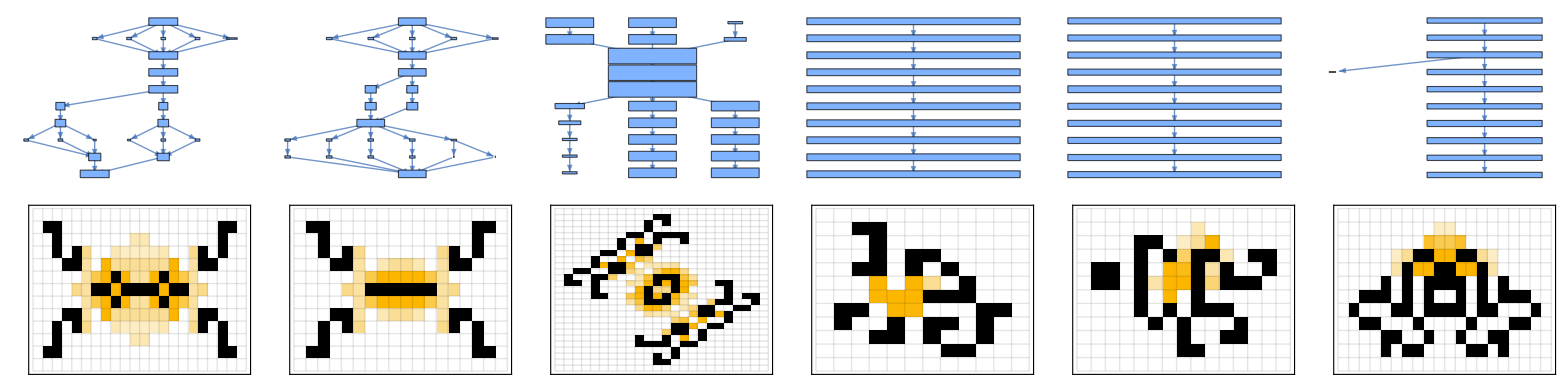
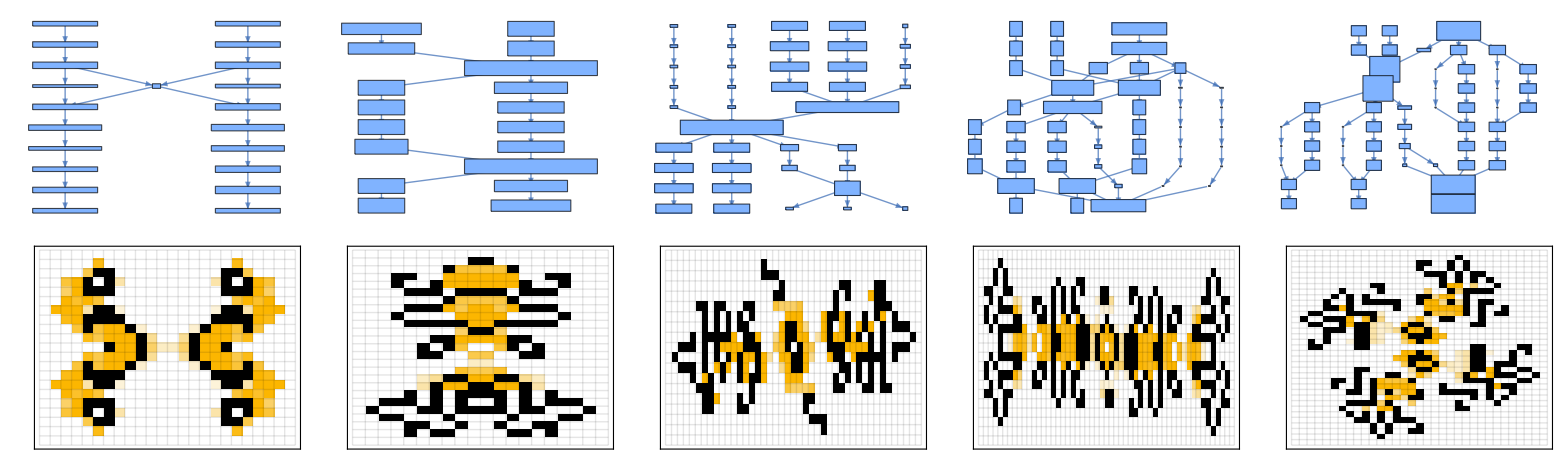

```mathematica
vertfunc = Function[{pos,val,blah},Rectangle[pos-#/45,pos+#/45]&@(Subtract@@(Reverse@MinMax[#])&/@Transpose[Ramp[val[[-1]]]])];
Style[Row[With[{elems=With[{data=Select[ResourceData["LifeWiki Dataset 2025"],#Class === "Oscillator" && #Period ==9&]},MapIndexed[{Graph[{{"[◼]", "BoundingBoxLayeredGraph"}}[#, Automatic, VertexShapeFunction->vertfunc],ImageSize->{Automatic,130}],{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#MatrixData,0},9,ImageSize->13Sqrt[Reverse@Dimensions[#1["MatrixData"]]], Frame->True,FrameStyle->If[4<=#2[[1]]<=5, Red, Automatic]]}&,Values[SortBy[data//Quiet,#Year&]]]]},Grid[Transpose[#],Frame->{All,True},(*Frame->All,*)FrameStyle->{GrayLevel[.3], 4->Red, 5->Red},Alignment->Center]&/@Partition[elems, UpTo[6]]]],LineSpacing->{1,40}]
```